```mathematica
$ProcessorCount
```

4

```mathematica
time=AbsoluteTime[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Import data *)
(**HVDARL**)
NamData0=Import["HVDARL/Rhos.txt","Table"];
```

```mathematica
Rho[i_]:={{NamData0[[4+16i,1]],NamData0[[5+16i,1]]},{NamData0[[6+16i,1]],NamData0[[7+16i,1]]}}+{{NamData0[[9+16i,1]],NamData0[[10+16i,1]]},{NamData0[[11+16i,1]],NamData0[[12+16i,1]]}}*I
RhoList1=ParallelTable[Rho[i],{i,0,NamData0[[1,1]]-1}];
```

```mathematica
RhoVPP[i_]:={{NamData0[[2+16i,1]]},{NamData0[[4+16i,1]],NamData0[[5+16i,1]]},{NamData0[[6+16i,1]],NamData0[[7+16i,1]]}}+{{0},{NamData0[[9+16i,1]],NamData0[[10+16i,1]]},{NamData0[[11+16i,1]],NamData0[[12+16i,1]]}}*I
RhoVPP2[i_]:={NamData0[[2+16i,1]],RhoList1[[i]]//MatrixForm}//MatrixForm
RhoVPPList1=ParallelTable[RhoVPP2[i],{i,0,NamData0[[1,1]]-1}];
```

```mathematica
(* Target HVDARL states *)
StateH={{1},{0}};
StateV={{0},{1}};
StateD=(1/(2^(1/2))){{1},{1}};
StateA=(1/(2^(1/2))){{1},{-1}};
StateR=(1/(2^(1/2))){{1},{I}};
StateL=(1/(2^(1/2))){{1},{-I}};
States = {StateH, StateV, StateD, StateA, StateR, StateL};
Dimensions[States]
```

{6,2,1}

```mathematica
StateToRho[i_]:=States[[i]].ConjugateTranspose[States[[i]]]
Rhos=ParallelTable[StateToRho[i],{i,1,Dimensions[States][[1]]}];
Dimensions[Rhos]
```

{6,2,2}

```mathematica
RhoTarget=Rhos
```

{{{1,0},{0,0}},{{0,0},{0,1}},{{1/2,1/2},{1/2,1/2}},{{1/2,-1/2},{-1/2,1/2}},{{1/2,-ⅈ/2},{ⅈ/2,1/2}},{{1/2,ⅈ/2},{-ⅈ/2,1/2}}}

```mathematica
sigma2={{0,1},{1,0}};
sigma3={{0,-I},{I,0}};
sigma1={{1,0},{0,-1}};
sigma={sigma1,sigma2,sigma3};blochStates[i_,x_]:=ConjugateTranspose[States[[x]]].sigma[[i]].States[[x]]
blochlistStates=ParallelTable[ Re[blochStates[i,x][[1,1]]],{x,1,Dimensions[States][[1]]},{i,1,3}  ];
```

```mathematica
(* Fidelity *)
Fidelity[Rho1_,Rho2_,i_,j_]:=Re[Tr[MatrixPower[MatrixPower[Rho1[[i]],1/2].Rho2[[j]].MatrixPower[Rho1[[i]],1/2],1/2]]]^2
```

```mathematica
FidelityList1=ParallelTable[Fidelity[RhoTarget,RhoList1,i,j],{j,1,Dimensions[RhoList1][[1]]},{i,1,Dimensions[RhoTarget][[1]]}];FidelityListTrans1=Transpose[FidelityList1];PosTable1=ParallelTable[Position[FidelityListTrans1,Max[FidelityListTrans1[[i]]]],{i,1,Dimensions[FidelityListTrans1][[1]]}];BestFidelitys1=ParallelTable[FidelityList1[[PosTable1[[i,1,2]],PosTable1[[i,1,1]]]],{i,1,Dimensions[PosTable1][[1]]}];
```

```mathematica
Sum[FidelityList1[[PosTable1[[i,1,2]],PosTable1[[i,1,1]]]],{i,1,Dimensions[PosTable1][[1]]}];
BestRhoList1=ParallelTable[RhoList1[[PosTable1[[i,1,2]]]],{i,1,Dimensions[PosTable1][[1]]}];
```

```mathematica
RhoToBloch[Rho_,i_,j_]:=Re[Tr[Rho[[i]].sigma[[j]]]]
```

```mathematica
BlochList1=ParallelTable[RhoToBloch[RhoList1,i,j],{i,1,Dimensions[RhoList1][[1]]},{j,1,Dimensions[sigma][[1]]}];
blochlistStates=ParallelTable[RhoToBloch[Rhos,i,j],{i,1,Dimensions[Rhos][[1]]},{j,1,Dimensions[sigma][[1]]}];
BestStates1=ParallelTable[RhoToBloch[BestRhoList1,i,j],{i,1,Dimensions[BestRhoList1][[1]]},{j,1,Dimensions[sigma][[1]]}];
```

```mathematica
(* AVG fidelity *)
```

```mathematica
BestFidelitys1
Max[BestFidelitys1]
Min[BestFidelitys1]
StandardDeviation[BestFidelitys1]
```

{0.999765,0.999702,0.999985,0.999426,0.99883,0.999016}

0.999985

0.99883

0.000452124

```mathematica
Sum[BestFidelitys1[[i]],{i,1,6}]/Dimensions[BestFidelitys1][[1]]
```

0.999454

```mathematica
(* AVG purity *)
```

```mathematica
Purity[Rho_]:=Re[Tr[MatrixPower[Rho,2]]]
```

```mathematica
BestPuritys1=ParallelTable[Purity[BestRhoList1[[i]]],{i,1,Dimensions[BestRhoList1][[1]]}]
Max[BestPuritys1]
Min[BestPuritys1]
StandardDeviation[BestPuritys1]
```

{1.,1.,1.,1.,0.999274,0.998921}

1.

0.998921

0.000478979

```mathematica
Sum[BestPuritys1[[i]],{i,1,Dimensions[BestPuritys1][[1]]}]/Dimensions[BestPuritys1][[1]]
```

0.999699

```mathematica
(* Angles *)
```

```mathematica
Angles1=Table[VectorAngle[BestStates1[[i]],blochlistStates[[i]]],{i,1,6}]
```

{0.0306755,0.0345095,0.00778653,0.0478983,0.05684,0.0422}

```mathematica
StandardDeviation[Angles1]
```

0.0169608

```mathematica
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]
```

0.971781 °

```mathematica
%/2
```

0.48589 °

```mathematica
Sum[Angles1[[i]],{i,1,Dimensions[Angles1][[1]]}]/Dimensions[Angles1][[1]]
```

0.0366516

```mathematica
UnitConvert[Quantity[%, "Radians"], "AngularDegrees"]
```

2.09998 °

```mathematica
%/2
```

1.04999 °

```mathematica
(* Hammer proj. *)
GetSpherical[Bloch_]:={ArcTan[Sqrt[Bloch[[2]]^2+Bloch[[1]]^2],Bloch[[3]]],Limit[ArcTan[x,Bloch[[2]]],{x->Bloch[[1]]}]}
```

```mathematica
HammerCoordinates[bloch_]:=ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->GetSpherical[bloch][[1]],az->GetSpherical[bloch][[2]]},{2}]
```

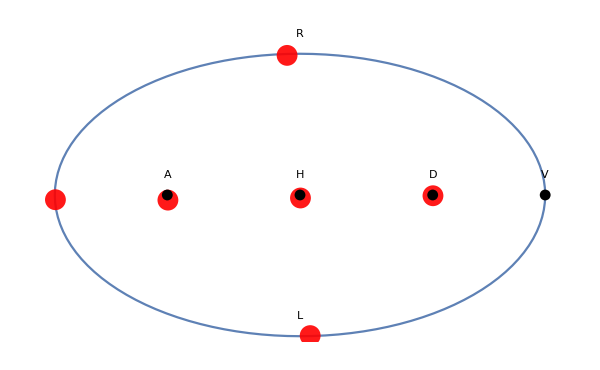

```mathematica
Show[ListPlot[Table[ArrayReshape[{(2*Sqrt[2] * Cos[elev]*Sin[az/2])/Sqrt[1+Cos[elev] Cos[az/2]],(Sqrt[2] * Sin[elev])/Sqrt[1+Cos[elev] Cos[az/2]]}/.{elev->Range[0.,2*Pi,2*Pi/120][[i]],az->Pi},{2}],{i,1,121}],Joined->{True,False}],
ListPlot[Table[HammerCoordinates[BestStates1[[i]]],{i,1,6}],PlotStyle->{PointSize[0.025],RGBColor[1,0,0],Opacity[0.9]}],ListPlot[Table[HammerCoordinates[blochlistStates[[i]]],{i,1,6}],PlotStyle->{PointSize[0.013],RGBColor[0,0,0]}],
Graphics[Style[Text["H",{0,0.2}],Black,Italic,30]],
Graphics[Style[Text["V",{2 √2,0.2}],Black,Italic,30]],
Graphics[Style[Text["D",{2/(√(1+1/(√2))),0.2}],Black,Italic,30]],
Graphics[Style[Text["A",{-2/(√(1+1/(√2))),0.2}],Black,Italic,30]],
Graphics[Style[Text["R",{0,√2+0.2}],Black,Italic,30]],
Graphics[Style[Text["L",{0,-√2+0.2}],Black,Italic,30]],
PlotRange->All,Axes->False,ImageSize->600]
```